```mathematica
tdE1[0.05,ξc,-1,10^(-100)]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 50 recursive bisections in y near {y} = {0.99999999999999999999999999999999997183794651514220967435569}. NIntegrate obtained 0.00661482724711091532076960385974731683678898961842843281737552 ⅈ and 0.000887143124859562974646321888193671654433019340085199768127621 for the integral and error estimates.

0.006614827247 ⅈ

```mathematica
tdE1[0.05,ξc,-1,10^(-11)]
```

0.003752110399 ⅈ

```mathematica
tdE1[0.05,ξc,-1,10^(-10)]
```

0.003469387124 ⅈ

```mathematica
tdE1[0.05,ξc,-1,10^(-9)]
```

0.003186663846 ⅈ

```mathematica
tdE1[0.05,ξc,-1,10^(-5)]
```

0.002055727054 ⅈ

```mathematica
tdE1[0.05,ξc,-1,10^(-2)]
```

0.001160753713 ⅈ

```mathematica
10^(-2)
```

1/100

```mathematica
N[1/100]
```

0.01

```mathematica
tdE1[0.05,ξc,-1,10^(-11)]+tdE2[0.05,ξc,-1,10^(-11)]
```

0.00116615623 ⅈ

```mathematica
tdE1[0.05,ξc,-1,10^(-9)]+tdE2[0.05,ξc,-1,10^(-9)]
```

0.00116615618 ⅈ

```mathematica
tdE1[0.05,ξc,-1,10^(-5)]+tdE2[0.05,ξc,-1,10^(-5)]
```

0.00116606883 ⅈ

```mathematica
EDtermuda[-0.01,0.1,-1]
```

1/(1-y)0.0326303 InterpolatingFunction[…][y,-1]

```mathematica
0.03263032883927614*InterpolatingFunction[…][0.95,-1]
```

0.-0.000146196 ⅈ

InterpolatingFunction::dmval: Input value {0.900004,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

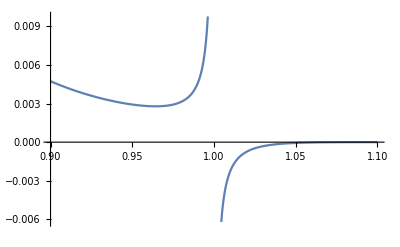

```mathematica
Plot[I*EDtermuda[-0.01,0.1,-1],{y,1-0.1,1+0.1}]
```

InterpolatingFunction::dmval: Input value {0.900004,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

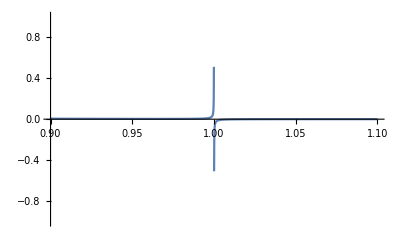

```mathematica
Plot[I*EDtermuda[-0.01,0.1,-1],{y,1-0.1,1+0.1},PlotRange->{Automatic,{-1,1}}]
```

InterpolatingFunction::dmval: Input value {0.900002,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

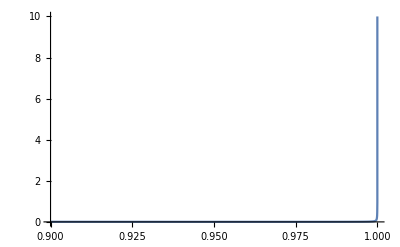

```mathematica
Plot[I*EDtermuda[-0.01,0.1,-1],{y,1-0.1,1},PlotRange->{Automatic,{0,10}}]
```

```mathematica
EDtermuda[-0.01,0.1,-1]/.{y->1-10^(-12)}
```

0.-3.24153×10^7 ⅈ

```mathematica
NIntegrate[1/x,{x,-0.1,-0.0000000000000001}]
```

-34.5388

```mathematica
NIntegrate[(0.001)/x,{x,-0.1,-0.0000001}]
```

-0.00138155

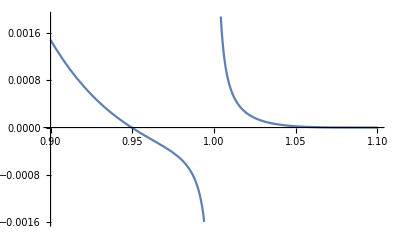

```mathematica
Plot[-I*HDtermuda[-0.01,0.1,-1],{y,1-0.1,1+0.1}]
```

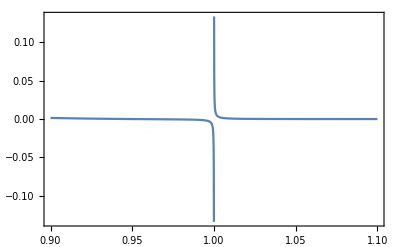
-Graphics-H_uy

```mathematica
hd=Labeled[Show[Plot[-I*HDtermuda[-0.01,0.1,-1],{y,1-0.1,1+0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],{"H_u","y"},{Left,Bottom}]
```

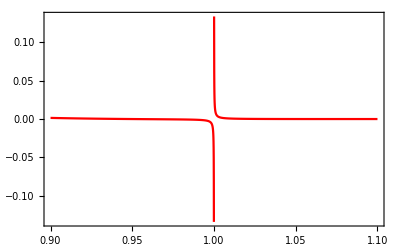
-Graphics-H_uy

```mathematica
hd2=Labeled[Show[Plot[-I*HDtermuda[-0.01,0.1,-1],{y,1-0.1,1+0.1},PlotRange->All,PlotStyle->Red],Frame->True,FrameStyle->Directive[Thick,20]],{"H_u","y"},{Left,Bottom}]
```

```mathematica
pathh2dD=FileNameJoin[{"G:\\calc-online\\gpd\\juanjiclac\\juanji\\Dtermtest\\re",
"hd-b-2d.pdf"}];
Export[pathh2dD,hd2]
```

G:\calc-online\gpd\juanjiclac\juanji\Dtermtest\re\hd-b-2d.pdf

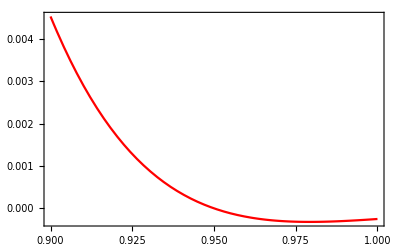
-Graphics-fy

```mathematica
fd=Labeled[Show[Plot[-I*sf2[y,-1],{y,1-0.1,1},PlotStyle->Red],Frame->True,FrameStyle->Directive[Thick,20]],{"f","y"},{Left,Bottom}]
```

```mathematica
pathh2df=FileNameJoin[{"G:\\calc-online\\gpd\\juanjiclac\\juanji\\Dtermtest\\re",
"f-b-2d.pdf"}];
Export[pathh2df,fd]
```

G:\calc-online\gpd\juanjiclac\juanji\Dtermtest\re\f-b-2d.pdf

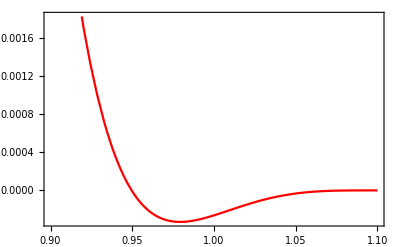
-Graphics-fy

```mathematica
fd2=Labeled[Show[Plot[-I*sf2[y,-1],{y,1-0.1,1+0.1},PlotStyle->Red],Frame->True,FrameStyle->Directive[Thick,20]],{"f","y"},{Left,Bottom}]
```

```mathematica
pathh2df2=FileNameJoin[{"G:\\calc-online\\gpd\\juanjiclac\\juanji\\Dtermtest\\re",
"f-b-2d-full.pdf"}];
Export[pathh2df2,fd2]
```

G:\calc-online\gpd\juanjiclac\juanji\Dtermtest\re\f-b-2d-full.pdf

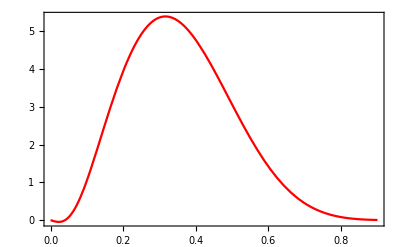
-Graphics-fy

```mathematica
fd3=Labeled[Show[Plot[-I*sf1[y,-1],{y,0,1-0.1},PlotStyle->Red],Plot[-I*sf2[y,-1],{y,1-0.1,1+0.1},PlotStyle->Red],Frame->True,FrameStyle->Directive[Thick,20]],{"f","y"},{Left,Bottom}]
```

```mathematica
sf1[1,-1]
```

InterpolatingFunction::dmval: Input value {1,-1} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.-0.0127517 ⅈ

```mathematica
0.03263032883927614*0.001
```

0.0000326303

```mathematica
0.03263032883927614*0.005
```

0.000163152

```mathematica
NIntegrate[1/x,{x,-0.1,-10^(-60)}]
```

-135.853

```mathematica
Precision
```

```mathematica
NIntegrate[1/x,{x,-0.1,-10^(-2)}]
```

-2.30259

```mathematica
NIntegrate[1/x,{x,-0.1,-10^(-10)}]
```

-20.7233

```mathematica
-I*(tdH1[-0.01,0.1,-1,0.01]+tdH2[-0.01,0.1,-1,0.01])
```

0.00002284065045

```mathematica
-I*(tdH1[-0.01,0.1,-1,10^(-4)]+tdH2[-0.01,0.1,-1,10^(-4)])
```

0.0000194100444

```mathematica
-I*(tdH1[-0.01,0.1,-1,10^(-6)]+tdH2[-0.01,0.1,-1,10^(-6)])
```

0.0000193752819

```mathematica
-I*(tdH1[-0.01,0.1,-1,10^(-8)]+tdH2[-0.01,0.1,-1,10^(-8)])
```

0.000019374934

```mathematica
-I*(tdH1[-0.01,0.1,-1,10^(-10)]+tdH2[-0.01,0.1,-1,10^(-10)])
```

0.000019374931

```mathematica
-I*tdH1[-0.01,0.1,-1,0.01]
```

0.00001580367639

```mathematica
-I*tdH1[-0.01,0.1,-1,10^(-4)]
```

-0.00002524554336

```mathematica
-I*tdH1[-0.01,0.1,-1,10^(-6)]
```

-0.00006466894493

```mathematica
-I*tdH1[-0.01,0.1,-1,10^(-8)]
```

-0.0001040750182

```mathematica
-I*tdH1[-0.01,0.1,-1,10^(-10)]
```

-0.0001434809205